```mathematica
Evals=Flatten[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/Eigenvals.dat"]];
```

```mathematica
Ecutoff=Evals[[3]]
```

-43.2109

```mathematica
Evals=Sort[Drop[Evals,1;;3]];
Evals[[1;;10]]
```

{5.48698×10^6,5.48698×10^6,5.48698×10^6,5.48698×10^6,4.41853×10^6,4.41853×10^6,4.41853×10^6,4.41853×10^6,4.41853×10^6,4.41853×10^6}

```mathematica
Sort[Evals];
```

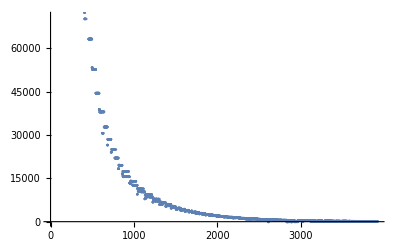

```mathematica
ListPlot[Evals]
```

```mathematica
eValsBound = Sort[Select[Evals,-70<#<Ecutoff&]]
```

{-64.8373,-64.1741,-63.8175,-63.4813,-63.0111,-61.6667,-60.5479,-59.0957,-53.9798,-52.8963,-52.5799,-51.1006,-50.6992,-50.1564,-50.01,-49.8528,-49.0756,-49.0119,-48.5567,-48.4786,-47.7069,-46.1157,-45.5583,-45.3328,-44.8236,-44.4264,-43.8629,-43.5506}

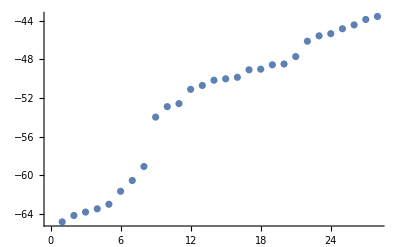

```mathematica
ListPlot[eValsBound]
```

```mathematica
Es=Table[eValsBound[[i+1]]-eValsBound[[i]],{i,1,Length[eValsBound]-1}]
```

{0.663177,0.356614,0.336172,0.470274,1.34438,1.11879,1.45221,5.11589,1.08347,0.316395,1.47932,0.401353,0.542859,0.146415,0.157168,0.777177,0.063725,0.455172,0.078097,0.771697,1.5912,0.557422,0.225475,0.509203,0.397283,0.563486,0.312222}

```mathematica
eTrim = Select[Es,#>0.0000001&];
avg = Mean[eTrim]
eTrim = eTrim/avg
Sort[eTrim]
Length[Es]
Length[eTrim]
```

0.788394

{0.841174,0.45233,0.426401,0.596496,1.70521,1.41907,1.84198,6.489,1.37428,0.401315,1.87637,0.509077,0.688563,0.185713,0.199352,0.985772,0.0808288,0.577341,0.0990583,0.978821,2.01828,0.707035,0.285992,0.645874,0.503914,0.714726,0.396023}

{0.0808288,0.0990583,0.185713,0.199352,0.285992,0.396023,0.401315,0.426401,0.45233,0.503914,0.509077,0.577341,0.596496,0.645874,0.688563,0.707035,0.714726,0.841174,0.978821,0.985772,1.37428,1.41907,1.70521,1.84198,1.87637,2.01828,6.489}

27

27

```mathematica
bins=Table[x,{x,0,5,0.2}];
```

```mathematica
bFit=Table[0.5*(bins[[i]]+bins[[i+1]]),{i,1,Length[bins]-1}];
```

```mathematica
EspaceBin=BinCounts[eTrim,{bins}];
```

```mathematica
NormBrodyBinCs=Table[EspaceBin[[i]]/Total[EspaceBin]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
```

```mathematica
Remove[al,p]
```

```mathematica
alpha[q_]:=(Gamma[(q+2)/(q+1)])^(q+1)
```

```mathematica
p[q_,s_]:=alpha[q]*(q+1)*s^(q)*E^(-alpha[q]*s^(q+1))
```

```mathematica
brodyPdist = Table[{bFit[[i]],NormBrodyBinCs[[i]]},{i,1,Length[bFit]}]
```

{{0.1,0.769231},{0.3,0.384615},{0.5,1.34615},{0.7,0.769231},{0.9,0.576923},{1.1,0.},{1.3,0.192308},{1.5,0.192308},{1.7,0.192308},{1.9,0.384615},{2.1,0.192308},{2.3,0.},{2.5,0.},{2.7,0.},{2.9,0.},{3.1,0.},{3.3,0.},{3.5,0.},{3.7,0.},{3.9,0.},{4.1,0.},{4.3,0.},{4.5,0.},{4.7,0.},{4.9,0.}}

```mathematica
p1=ListPlot[brodyPdist,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->Red];
```

```mathematica
pars = FindFit[brodyPdist,{p[q,s],q>0,q<1},{q},s]
```

{q→0.205224}

```mathematica
p2=Plot[p[q/.pars,s],{s,0,5},PlotRange->All,PlotStyle->Red];
```

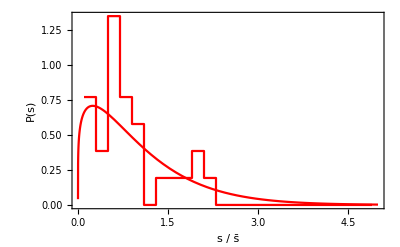

```mathematica
p40=Show[p1,p2,PlotRange->All,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

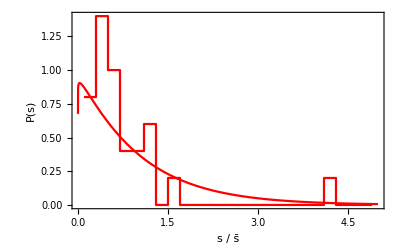

```mathematica
p20=Show[p1,p2,PlotRange->All,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```